```mathematica
R:=9
M:=2
ρ0:=3M/(4 π R^3)
eqnsM:={m'[r]==4*π*r^2*ρ0}
condM:={m[0]==0}
systemM=Join[eqnsM,condM]
DSolve[systemM, {m[r]}, {r}]
```

{m'[r]==(2 r^2)/243,m[0]==0}

{{m[r]→(2 r^3)/729}}

m[r]/ρ

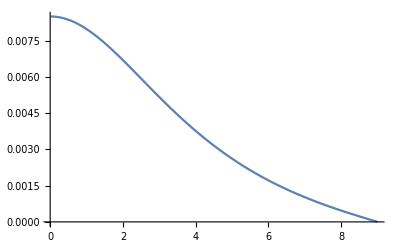

```mathematica
R:=9
M:=3.9
ρ0:=3M/(4 π R^3)
m[r]:=4/3 π r^3 ρ0
my0=0.01;
pc:=ρ0*(1-(1-2M/R)^(1/2))/(3*(1-2M/R)^(1/2)-1)
eqnP:={-p'[r]==(ρ0+p[r])*(m[r]+4*π*r^3*p[r])/(r^2*(1-2*m[r]/r))}
condP:={p[my0]==pc}
systemP:=Join[eqnP,condP]
state=First[NDSolve`ProcessEquations[systemP, {p}, {r, my0, R}]];
NDSolve`Iterate[state,R]
sol=NDSolve`ProcessSolutions[state];
(*sol=NDSolve[systemP,p,{r,my0,R}]*)
Plot[Evaluate[p[r]/.sol],{r,my0,R}]
```